```mathematica
(* ResourceFunction["MaTeXInstall"][] *)
```

```mathematica
<<MaTeX`
ConfigureMaTeX["pdfLaTeX"-> "/Library/TeX/texbin/pdflatex"];
ConfigureMaTeX["Ghostscript"-> "/usr/local/bin/gs"];
```

```mathematica
MaTeX@HoldForm[χ]
```

# Error Estimate Notebooks

This notebook produces figures and certain equations in arXiv:2010.09509 

The plots section reproduces Fig 1 and Fig 3 and error estimates in Appendix A

```mathematica
Ep=1/2 Eγ (1+ √(1-((m★)/Eγ)^2) √(1-((2me)/(m★))^2)cosϑ);
Solve[(Ep/. cosϑ-> 1)==λp,m★]//Simplify;
pointSub={%⟦2⟧,%⟦4⟧};
Clear[Ep]
pointSub=pointSub/.λp-> Ep
```

{{m★→√2 √(-Ep^2+Ep Eγ+me^2-√((Ep^2-me^2) (Ep^2-2 Ep Eγ+Eγ^2-me^2)))},{m★→√2 √(-Ep^2+Ep Eγ+me^2+√((Ep^2-me^2) (Ep^2-2 Ep Eγ+Eγ^2-me^2)))}}

```mathematica
{mMin,mMax}=m★/. pointSub/.me->ϵ Eγ/. Ep-> Eγ(  (1-δ) -ϵ  )/.Eγ-> 1//FullSimplify
```

{√2 √(ϵ-δ (-1+δ+2 ϵ)-√((-1+δ) δ (-1+δ+2 ϵ) (δ+2 ϵ))),√2 √(ϵ-δ (-1+δ+2 ϵ)+√((-1+δ) δ (-1+δ+2 ϵ) (δ+2 ϵ)))}

## Appendix A

### Run this first

```mathematica
cosϑ= (1-2δ-2ϵ)/(βe β★);
sub1=(Normal@Series[((1-cosϑ^2)βe^2//Simplify)/.( 2 δ+2 ϵ-1)^2-> 1 - 4(δ+ϵ)/.β★-> 1-1/2 f★/. βe-> 1-1/2 fe,{fe,0,1},{f★,0,1}]//Simplify)/.{fe->(4 me^2)/(m★)^2,f★->(m★)^2/Eγ^2}/.(m★)^2 (4 δ+4 ϵ-1)-> -(m★)^2//Simplify;
sub2=Normal@Series[((1-cosϑ^2 βe^2)//Simplify)/.( 2 δ+2 ϵ-1)^2-> 1 - 4(δ+ϵ)/.β★-> 1-1/2 f★/. βe-> 1-1/2 fe,{fe,0,1},{f★,0,1}]/.{fe->(4 me^2)/(m★)^2,f★->(m★)^2/Eγ^2}/.(m★)^2 (4 δ+4 ϵ-1)-> -(m★)^2//Simplify;
Print["(1-cosϑ^2)βe^2~   ", sub1, " +O(δ^2,ϵ^2)"]
```

(1-cosϑ^2)βe^2~   -(4 me^2)/(m★)^2-(m★)^2/Eγ^2+4 (δ+ϵ) +O(δ^2,ϵ^2)

^^^  These appear in Eqs (A10) and (A11) . 

Now start from Eq (35) . Set  F_* = 1 then use the substitutions defined above and drop higher order terms.

```mathematica
Series[2/4((2CT (m★)^2/Eγ^2-(1-cosθ^2)βe^2)+2(1-cosθ^2 βe^2)CL)/.{(1-cosθ^2)βe^2-> sub1, (1-cosθ^2 βe^2)-> sub2}//Expand,{m★,0,2}]/. (me/Eγ)^2-> 0//FullSimplify
```

(2 me^2)/(m★)^2+2 (-1+2 CL) (δ+ϵ)+((1-2 CL+2 CT) (m★)^2)/(2 Eγ^2)+O[m★]^3

```mathematica
Series[1/4(2m★ dm★)/(m★)^2((2-(1-cosθ^2)βe^2)(1+CT (m★)^2/Eγ^2)+2(1-cosθ^2 βe^2)CL)-1/4(2m★ dm★)/(m★)^2 2 /.{(1-cosθ^2)βe^2-> sub1, (1-cosθ^2 βe^2)-> sub2}//Expand,{m★,0,2}]//Simplify;
integrandA9=(m★)/(dm★)Expand[%]/.me^2/Eγ^2-> 0 //Simplify
```

(2 me^2)/(m★)^2+2 (-1+2 CL) (δ+ϵ)+((1-2 CL+CT (2-4 δ-4 ϵ)) (m★)^2)/(2 Eγ^2)+O[m★]^4

Now integrate for (m_*)^(-) to (m_*)^(+) ( I do this “by hand”  just to keep the formula’s formatting nice)

```mathematica
integralA10=  me^2(1/(m★m)^2-1/(m★p)^2) + 2(2CL-1)(δ+ϵ)Log[(m★p)/(m★m)]+(-2 CL+CT (-4 δ-4 ϵ+2)+1)/4((m★p)^2/Eγ^2-(m★m)^2/Eγ^2)
```

me^2 (1/(m★m)^2-1/(m★p)^2)+1/4 (-(m★m)^2/Eγ^2+(m★p)^2/Eγ^2) (1-2 CL+CT (2-4 δ-4 ϵ))+2 (-1+2 CL) (δ+ϵ) Log[(m★p)/(m★m)]

Check that there are no stupid typos

```mathematica
integralA10-Integrate[1/(m★)integrandA9,{m★,m★m,m★p}]/. {m★p-> RandomReal[],m★m-> RandomReal[]}//Simplify
```

0.-8.88178×10^-16 me^2+(-3.46945×10^-18+6.93889×10^-18 CL+CT (-6.93889×10^-18+1.38778×10^-17 δ+1.38778×10^-17 ϵ))/Eγ^2

### Relativistic electron (δ ≫ ϵ )

We have that 
(m_★)^(+) ~ √(4 δ) 
(m_★)^(-) ~ √(ϵ^2/δ)

```mathematica
(Assuming[δ>0,Series[#,{δ,0,3}]]&)/@({mMin^2}/.ϵ-> e δ^2)//Simplify
(Assuming[δ>0,Series[#,{δ,0,3}]]&)/@({mMax^2}/.ϵ-> e δ^2)//Simplify
```

{e^2 δ^3+O[δ]^(7/2)}

{4 δ+4 (-1+e) δ^2-e (8+e) δ^3+O[δ]^(7/2)}

Now we sub this into integralA10

```mathematica
Simplify@Normal@Series[Simplify[integralA10/.{m★p->  Eγ √(4δ),m★m-> Eγ √(ϵ^2/δ),me-> ϵ Eγ},{δ>0,ϵ>0}]/.ϵ-> e δ^2,{δ,0,1}]/. e-> ϵ/δ^2
```

2 δ (1-CL+CT+(-1+2 CL) Log[(2 δ)/ϵ])

### Quasi-Relativistic electron (δ ~ ϵ )

```mathematica
subm=m★m->Eγ Sqrt@Normal[(Assuming[δ>0,Series[#,{δ,0,1}]]&)/@(mMin^2/.ϵ-> e δ )//Simplify]
subp=m★p-> Eγ Sqrt@Normal[(Assuming[δ>0,Series[#,{δ,0,1}]]&)/@(mMax^2/.ϵ-> e δ)//Simplify]
```

m★m→Eγ √((2+2 e-2 √(1+2 e)) δ)

m★p→√2 Eγ √((1+e+√(1+2 e)) δ)

```mathematica
me^2/(m★m)^2-me^2/(m★p)^2/.{subm,subp}/.me-> e δ Eγ//Simplify
(m★p)^2/Eγ^2-(m★m)^2/Eγ^2/.{subm,subp}/.me-> e δ Eγ//Simplify
```

√(1+2 e) δ

4 √(1+2 e) δ

```mathematica
Simplify@Normal@Series[Simplify[integralA10/.subm/.subp/.me-> ϵ Eγ,{δ>0,ϵ>0}]/.ϵ-> e δ,{δ,0,1}]
```

δ (√(1+2 e)+(1-2 CL+2 CT) √(1+2 e)+2 (-1+2 CL) (1+e) Log[(√(1+e+√(1+2 e)))/(√(1+e-√(1+2 e)))])

```mathematica
%/.e-> ϵ/δ//Simplify
```

δ √(1+(2 ϵ)/δ)+(1-2 CL+2 CT) δ √(1+(2 ϵ)/δ)+2 (-1+2 CL) (δ+ϵ) Log[(√(1+ϵ/δ+√(1+(2 ϵ)/δ)))/(√(1+ϵ/δ-√(1+(2 ϵ)/δ)))]

### Non-Relativistic electron (δ ≪ ϵ )

```mathematica
subm=m★m->Eγ Sqrt@Normal[(Assuming[ϵ>0,Series[#,{ϵ,0,2}]]&)/@(mMin^2/.δ-> d ϵ^2 )//Simplify]
subp=m★p-> Eγ Sqrt@Normal[(Assuming[ϵ>0,Series[#,{ϵ,0,2}]]&)/@(mMax^2/.δ-> d ϵ^2)//Simplify]
```

m★m→Eγ √(2 ϵ-2 √2 √d ϵ^(3/2)+2 d ϵ^2)

m★p→Eγ √(2 ϵ+2 √2 √d ϵ^(3/2)+2 d ϵ^2)

```mathematica
Assuming[ϵ>0,Simplify@Normal@Series[Simplify[integralA10/.subm/.subp/.me-> ϵ Eγ,{δ>0,ϵ>0}]/.δ-> d ϵ^2,{ϵ,0,2}]/. d-> δ/ϵ^2//Simplify]
```

2 √2 (CL+CT) √(δ ϵ)

## Plots

### Various photon energies

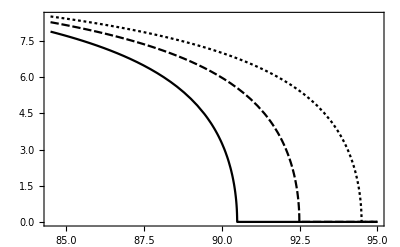

```mathematica
α=1/137;
ticks={ScientificForm[0.001]};
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};

Plot[{100000 α/(Eγ  π)HeavisideTheta[Eγ-me-Ep]Log[mMax/mMin]/. δ-> 1-(Ep  +me)/Eγ/. ϵ-> me/Ep/. {me-> 0.511,Eγ-> 91}//N,100000 α/(Eγ π)HeavisideTheta[Eγ-me-Ep]Log[mMax/mMin]/. δ-> 1-(Ep  +me)/Eγ/. ϵ-> me/Ep/. {me-> 0.511,Eγ-> 93}//N,100000 α/(Eγ π)HeavisideTheta[Eγ-me-Ep]Log[mMax/mMin]/. δ-> 1-(Ep  +me)/Eγ/. ϵ-> me/Ep/. {me-> 0.511,Eγ-> 95}//N},{Ep,84.489,95},BaseStyle->texStyle,PlotRange->Full,PlotTheme->"Monochrome", Frame-> True,FrameTicksStyle->{Automatic,Automatic},Axes->   False,PlotRangePadding-> {0,0.1 α/(100 π)},PlotLegends->Placed[(MaTeX[#,FontSize->13]&)/@{"\\bf E_\\gamma=91 ~\\textbf{MeV}","\\bf E_\\gamma=93 ~\\textbf{MeV}","\\bf E_\\gamma=95 ~\\textbf{MeV}"},{0.225,0.28}],FrameLabel->(MaTeX[#,FontSize->14]&)/@{"\\textbf{Positron Energy}~~~~~~~\\textbf{        [ MeV ]}","\\bf 10^5 \\times P_\\textbf{int}^{(0)}(E_+ | E_\\gamma)  ~~~~ [ \\textbf{MeV}^{-1} ]"},AspectRatio->1/GoldenRatio]
Clear[α]
```

### Estimating Errors Bands Gaussian

We take C_L and C_T to be uncorrelated and gaussian distributed such that their variance = 1

```mathematica
ΔPint=α/(Eγ π)HeavisideTheta[Eγ-me-Ep](integralA10/.{m★m->Eγ mMin,m★p->Eγ mMax} )/. δ-> 1-(Ep  +me)/Eγ/. ϵ-> me/Eγ/. {me-> 0.511,Eγ-> 100,α-> 1/137}//N;
p0Int=α/(Eγ π)HeavisideTheta[Eγ-me-Ep](Log[mMax/mMin]  )/. δ-> 1-(Ep  +me)/Eγ/. ϵ-> me/Eγ/. {me-> 0.511,Eγ-> 100,α-> 1/137}//N;
pIntPS=p0Int+ΔPint/. CL-> 0/.CT->0;
```

```mathematica
countM=0;
plotExprm=0;Do[myLocExpr=p0Int+ΔPint-pIntPS/.{CL->RandomVariate[NormalDistribution[] ],CT->RandomVariate[NormalDistribution[] ],α-> 1/137};
If[(myLocExpr/.Ep-> 90)<0,plotExprm=plotExprm+(myLocExpr-pIntPS)^2 ;
countM=countM+1],{n,1,1000}];
plotExprm=p0Int-√(2*plotExprm/1000);


plotExprp=0;Do[myLocExpr=p0Int+ΔPint-pIntPS/.{CL->RandomVariate[NormalDistribution[] ],CT->RandomVariate[NormalDistribution[] ],α-> 1/137};
If[(myLocExpr/.Ep-> 90)>0,plotExprp=plotExprp+(myLocExpr-pIntPS)^2 ],{n,1,1000}];
plotExprp=p0Int+√(2*plotExprp/1000);
```

```mathematica
tab=Table[p0Int+ΔPint/.{CT-> RandomVariate[NormalDistribution[] ],CL-> RandomVariate[NormalDistribution[] ]},{n,1,1000}];
```

```mathematica
pInt1σGauss=Interpolation[ ({#⟦1⟧,Sqrt[#⟦2⟧]}&)/@ Table[{Ep,Variance@tab},{Ep,85,100,0.5}] ][Ep];
```

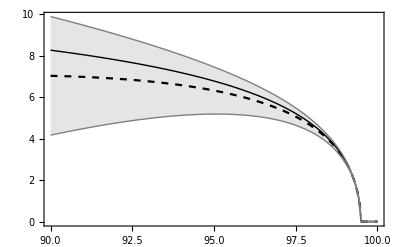

```mathematica
pGauss=Plot[{10^5 p0Int,10^5 pIntPS,10^5(pIntPS+pInt1σGauss),10^5(pIntPS-pInt1σGauss)},{Ep,90,100},PlotStyle->{{Black,Thick},{Black,Dashed},{Gray,Thin},{Gray,Thin}},Filling-> {3-> {4}},Frame-> True,FrameStyle->Black,FrameLabel->(MaTeX[#,FontSize->14]&)/@{"\\textbf{Positron Energy}~~~~~\\textbf{        [ MeV ]}","\\bf 10^5 \\times P_\\textbf{int}(E_+ | E_\\gamma)  ~~~ [ \\textbf{MeV}^{-1} ]"},PlotLegends->Placed[(MaTeX[#,FontSize->13]&)/@{"\\bf P_\\textbf{int}^{(0)}","\\bf P_\\textbf{int}^0 + \\Delta P_\\textbf{int},~~ C_L=C_T=0"},{0.4,0.265}]]
```

```mathematica
p0Expr/KWExpr/. Ep-> 95-0.511-0.0001
```

p0Expr/KWExpr

### Estimating Errors Bands Uniform

We take C_L and C_T to be uniformly distributed between [-√3, √3]  such that their variance = 1

```mathematica
ΔPint=α/(Eγ π)HeavisideTheta[Eγ-me-Ep](integralA10/.{m★m->Eγ mMin,m★p->Eγ mMax} )/. δ-> 1-(Ep  +me)/Eγ/. ϵ-> me/Eγ/. {me-> 0.511,Eγ-> 100,α-> 1/137}//N;
p0Int=α/(Eγ π)HeavisideTheta[Eγ-me-Ep](Log[mMax/mMin]  )/. δ-> 1-(Ep  +me)/Eγ/. ϵ-> me/Eγ/. {me-> 0.511,Eγ-> 100,α-> 1/137}//N;
pIntPS=p0Int+ΔPint/. CL-> 0/.CT->0;
```

```mathematica
countM=0;
plotExprm=0;Do[myLocExpr=p0Int+ΔPint-pIntPS/.{CL->√3 RandomReal[{-1,1}],CT->√3 RandomReal[{-1,1}],α-> 1/137};
If[(myLocExpr/.Ep-> 90)<0,plotExprm=plotExprm+(myLocExpr-pIntPS)^2 ;
countM=countM+1],{n,1,1000}];
plotExprm=p0Int-√(2*plotExprm/1000);


plotExprp=0;Do[myLocExpr=p0Int+ΔPint-pIntPS/.{CL->√3 RandomReal[{-1,1}],CT->√3 RandomReal[{-1,1}],α-> 1/137};
If[(myLocExpr/.Ep-> 90)>0,plotExprp=plotExprp+(myLocExpr-pIntPS)^2 ],{n,1,1000}];
plotExprp=p0Int+√(2*plotExprp/1000);
```

```mathematica
tab=Table[p0Int+ΔPint/.{CT-> RandomVariate[NormalDistribution[] ],CL-> RandomVariate[NormalDistribution[] ]},{n,1,1000}];
```

```mathematica
pInt1σUni=Interpolation[ ({#⟦1⟧,Sqrt[#⟦2⟧]}&)/@ Table[{Ep,Variance@tab},{Ep,85,100,0.5}] ][Ep];
```

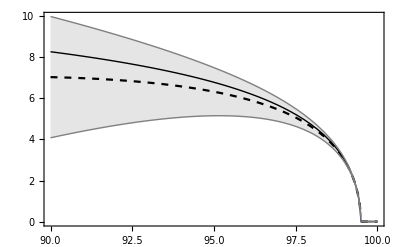

```mathematica
pUni=Plot[{10^5 p0Int,10^5 pIntPS,10^5(pIntPS+pInt1σUni),10^5(pIntPS-pInt1σUni)},{Ep,90,100},PlotStyle->{{Black,Thick},{Black,Dashed},{Gray,Thin},{Gray,Thin}},Filling-> {3-> {4}},Frame-> True,FrameStyle->Black,FrameLabel->(MaTeX[#,FontSize->14]&)/@{"\\textbf{Positron Energy}~~~~~\\textbf{        [ MeV ]}","\\bf 10^5 \\times P_\\textbf{int}(E_+ | E_\\gamma)  ~~~ [ \\textbf{MeV}^{-1} ]"},PlotLegends->Placed[(MaTeX[#,FontSize->13]&)/@{"\\bf P_\\textbf{int}^{(0)}","\\bf P_\\textbf{int}^0 + \\Delta P_\\textbf{int},~~ C_L=C_T=0"},{0.4,0.265}]]
```

### Comparison of Uniform vs Gauss

```mathematica
Show[pUni,pGauss]
```

-Graphics-

### Folded Spectrum

```mathematica
closureSpectrum=(1-2x +2 x^2)x(1-x)^2/. x-> Eγ/qmax/.qmax-> 100;mytabMid=Table[{Ep,NIntegrate[(closureSpectrum)p0Int,{Eγ,Ep+me/.me->  0.511,100}]},{Ep,90,100,0.011}]//Quiet; 
closureTab=Table[{Eγ,closureSpectrum},{Eγ,90,100}];
mytabLo=Table[{Ep,NIntegrate[(closureSpectrum)(pIntPS-pInt1σGauss),{Eγ,Ep+me/.me->  0.511,100}]},{Ep,90,100,0.011}]//Quiet;
mytabHi=Table[{Ep,NIntegrate[(closureSpectrum)(pIntPS+pInt1σGauss)//N,{Eγ,Ep+me/.me->  0.511,100}]},{Ep,90,100,0.011}]//Quiet;
```

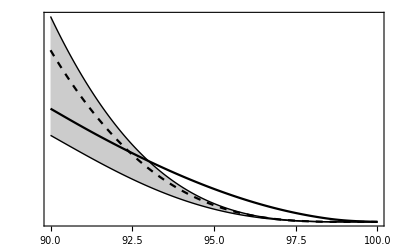

```mathematica
p1=ListPlot[{({#⟦1⟧,0.85#⟦2⟧}&)/@closureTab,({#⟦1⟧,5000#⟦2⟧}&)/@mytabMid,({#⟦1⟧,5000#⟦2⟧}&)/@mytabHi,({#⟦1⟧,5000#⟦2⟧}&)/@mytabLo},Joined->True,InterpolationOrder->2,PlotRange->Full,PlotStyle->{Black,{Black,Dashed},{Thin,Black},{Thin,Black}},Frame->True,FrameStyle->Black,Filling-> {3-> {4}},FrameLabel->(MaTeX[#,FontSize->14]&)/@{"\\textbf{Energy~~~~  [MeV]}",  "\\textbf{Spectral Shape ~[Linear Scale]}"},FrameTicks->{Automatic,None},PlotLegends->Placed[(MaTeX[#,FontSize->14]&)/@{"\\textbf{Photons}","\\textbf{Positrons/Electrons}"},{0.7,0.7}] ]
```

```mathematica
closureSpectrum=(1-2x +2 x^2)x(1-x)^2/. x-> Eγ/qmax/.qmax-> 100;
```

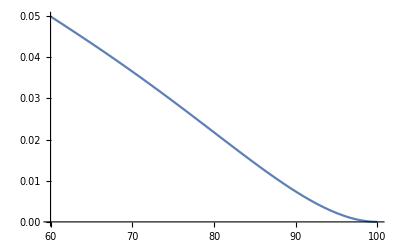

```mathematica
Plot[closureSpectrum,{Eγ,60,100}]
```